## 5

```mathematica
Integrate[1/(8 Pi)Exp[-r],{r,Infinity,0}]
%//N
```

-1/(8 π)

-0.0397887

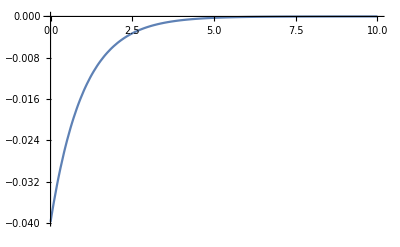

```mathematica
Plot [NIntegrate[1/(8 Pi)Exp[-r],{r,Infinity,x}],{x,0,10},PlotRange->All]
```

### Substitution

```mathematica
D[x/(x-1)^2,x]//Simplify
```

-(1+x)/(-1+x)^3

```mathematica
Integrate[(1+x)/(x-1)^3 1/(8 Pi)Exp[-x/(x-1)^2],{x,0,1}]
%//N
```

-1/(8 π)

-0.0397887

```mathematica
Limit[x/(x-1)^2,{x->1}]
```

∞

```mathematica
Integrate[(1+x)/(x-1)^3 1/(8 Pi)Exp[-x/(x-1)^2],{x,0,a}]
```

ConditionalExpression[(-1+ⅇ^(-a/(-1+a)^2))/(8 π), Re[a]≤1||a∉ℝ]

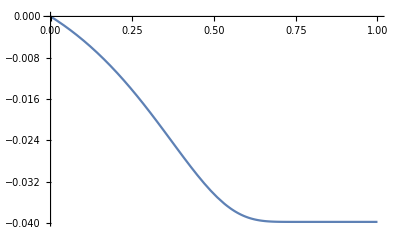

```mathematica
Plot[(-1+ⅇ^(-a/(-1+a)^2))/(8 π),{a,0,1}]
```

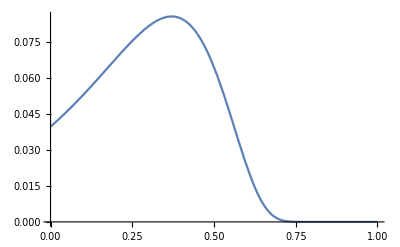

```mathematica
Plot[-(1+x)/(x-1)^3 1/(8 Pi)Exp[-x/(x-1)^2],{x,0,1},PlotRange->All]
```

NotebookDirectory::nosv: The notebook fetfy_shm is not saved.

SetDirectory::badfile: The specified argument, $Failed, should be a valid string or File.

Import::nffil: File poisson2.dat not found during Import.

0

ListLinePlot::lpn: $Failed is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[$Failed,PlotLegends→{Numerisch}],,].

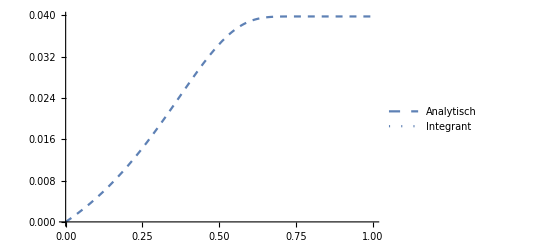
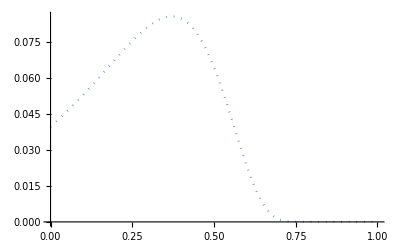
Show[ListLinePlot[$Failed,PlotLegends→{Numerisch}],-Graphics-,-Graphics-]

```mathematica
SetDirectory[NotebookDirectory[]];

PrintTemporary["make"];
Run["make"];

PrintTemporary["plot"];
d= Import["poisson2.dat"];
ByteCount[d]

Show[
{
ListLinePlot[d,PlotLegends->{"Numerisch"}],
Plot[-(-1+ⅇ^(-a/(-1+a)^2))/(8 π),{a,0,1},PlotStyle->Dashed,PlotLegends->{"Analytisch"}],
Plot[-(1+x)/(x-1)^3 1/(8 Pi)Exp[-x/(x-1)^2],{x,0,1},PlotStyle->Dotted,
PlotLegends->{"Integrant"}]
}
]

Export["img/poisson2.pdf",%];
```